Single Wavelength IFAC

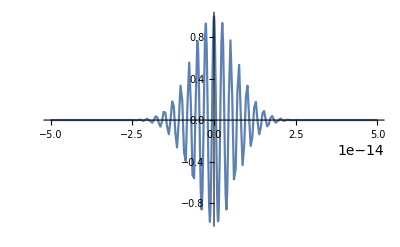

```mathematica
(*Unit definitions*)
n = 10^-9;
p = 10^-12;
f=10^-15;
lambda=760 n;
omega[lam_]:= 2*Pi*(3*10^8/lam);
tp=7*10^-15; (*Pulse width*)

w=omega[lambda];
e[t_]:=Exp[-I w t]Exp[-(t/tp)^2/2]
Plot[Re[e[t]],{t,-0.05p,0.05p},PlotRange->All]
```

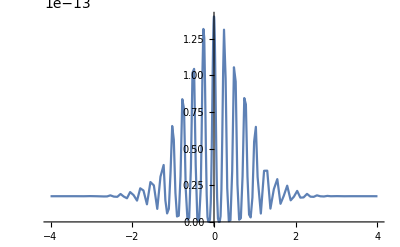

```mathematica
ifac[td_]:=NIntegrate[Abs[(e[t]+e[t-td])^2]^2,{t,-0.05p,0.05p} ]
Plot[ifac[td],{td,-40f,40f},PlotRange->All]
```

3-wavelength IFAC

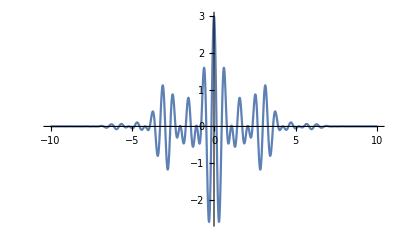

```mathematica
(*Pick 3 frequencies*)
w1=8;
w2=10;
w3=12;
(*Define the 3-frequency electric field*)
e3[t_,phi1_,phi2_,phi3_]:=(Exp[-I (w1 t+phi1)]+Exp[-I (w2 t+phi2)]+Exp[-I (w3 t+phi3)])*Exp[-t^2/10]
(*E-field plot*)
Plot[Re[e3[t,0,0,0]],{t,-10,10},PlotRange->All]
```

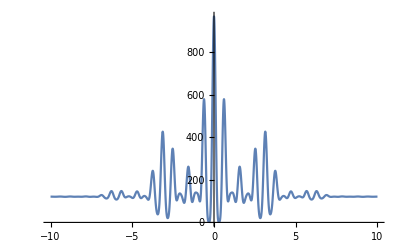

```mathematica
(*Interferometric AC plot*)
ifac3[td_,phi1_,phi2_,phi3_]:=NIntegrate[Abs[(e3[t,phi1,phi2,phi3]+e3[t-td,phi1,phi2,phi3])^2]^2,{t,-20 Pi,20Pi} ]
Plot[ifac3[td,0,0,0],{td,-10,10},PlotRange->All]
```

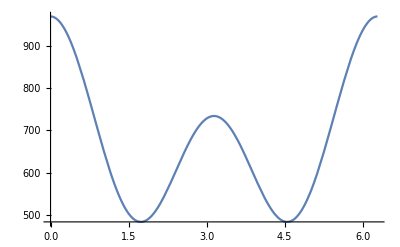

```mathematica
(*Variation of the TDZ Intensity with phi2*)
Plot[ifac3[0,0,phi2,0],{phi2,0,2 Pi},PlotRange->All]
```

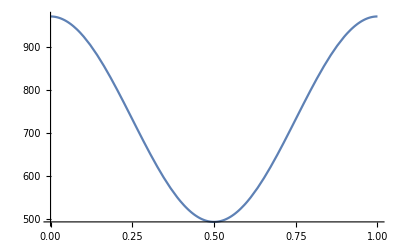

```mathematica
Plot[ifac3[0,2 Pi (0),2 Pi (0),2Pi phi3],{phi3,0,1},PlotRange->All]
```